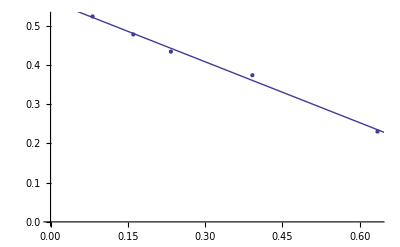

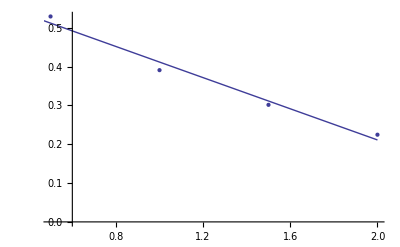

```mathematica
Subscript[ρ, pb] = 11.34*1000;
Subscript[ρ, al] = 2.70*1000;
i0 = 53963;
LeadThickness = {925.3,1821.3,2648.1,4441.7,7194.1}/Subscript[ρ, pb];
LeadPhotoCounts = {28231,25761,23397,20155,12417}/i0;
AluminumThickness = {1/2,1,3/2,2};
AluminumPhotoCounts = {28540,21082,16263,12113}/i0;
data=Transpose[{LeadThickness,LeadPhotoCounts}];
dp = ListPlot[data];
k = Fit[data,{1,x},x];
fp = Plot[k,{x,0,.7}];
Show[dp,fp]
data=Transpose[{AluminumThickness,AluminumPhotoCounts}];
dp = ListPlot[data];
k = Fit[data,{1,x},x];
fp = Plot[k,{x,0,2}];
Show[dp,fp]
```

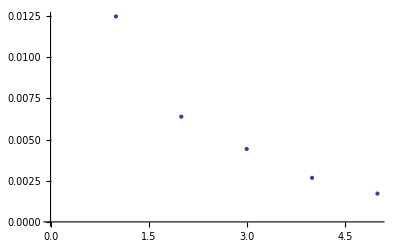

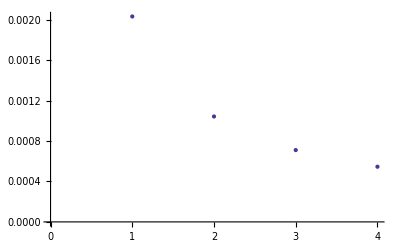

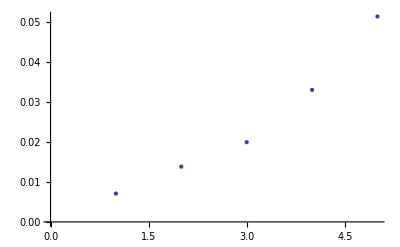

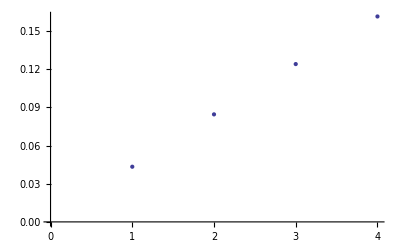

```mathematica
μ[L_,i_]:=(-Log[i/i0])/(Subscript[ρ, pb] L);
β[L_,i_]:=1/(μ[L,i] Subscript[ρ, pb]);
ListPlot[Table[μ[LeadThickness[[i]],LeadPhotoCounts[[i]]],{i,Length[LeadThickness]}]]
ListPlot[Table[μ[AluminumThickness[[i]],AluminumPhotoCounts[[i]]],{i,Length[AluminumPhotoCounts]}]]
ListPlot[Table[β[LeadThickness[[i]],LeadPhotoCounts[[i]]],{i,Length[LeadThickness]}]]
ListPlot[Table[β[AluminumThickness[[i]],AluminumPhotoCounts[[i]]],{i,Length[AluminumPhotoCounts]}]]
```